```mathematica
Integrate[ 1/j,{j,1,n}]
```

ConditionalExpression[Log[n],Re[n]≥0||n∉Reals]

```mathematica
Integrate[ 1/( j k),{j,1,n},{k,1,n/j}]
```

ConditionalExpression[Log[n]^2/2,Re[n]≥0||n∉Reals]

```mathematica
Integrate[ 1/( j k l),{j,1,n},{k,1,n/j}, {l,1,n/(j k)}]
```

ConditionalExpression[Log[n]^3/6,Re[n]≥0||n∉Reals]

```mathematica
Integrate[ 1/( j k l m),{j,1,n},{k,1,n/j}, {l,1,n/(j k)},{m,1,n/(j k l)}]
```

ConditionalExpression[Log[n]^4/24,Re[n]≥0||n∉Reals]

```mathematica
Sum[ (-1)^(k+1)/k Log[n]^k/k!,{k,1,Infinity}]
```

```mathematica
F[n_]:=EulerGamma+Gamma[0,Log[n]]+Log[Log[n]]
F2[n_]:=Gamma[0,Log[n]]
```

```mathematica
p[n_]:= FullSimplify[MangoldtLambda[n]/Log[n]]
```

```mathematica
S[n_]:=Sum[ If[p[j]≠0,p[j],0]/j,{j,2,n}]

S2[n_]:=Sum[ If[p[j]≠0,p[j],0]/(j^2),{j,2,n}]

S[25]
```

188126532397/107084577600

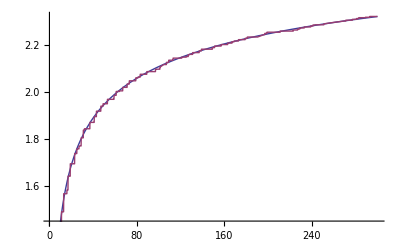

```mathematica
Plot[{F[n],S[n]},{n,1,300}]
```

```mathematica
Integrate[ 1/j^2,{j,1,n}]
```

ConditionalExpression[1-1/n,Re[n]≥0||n∉Reals]

```mathematica
Expand[Integrate[ 1/( j^2 k^2),{j,1,n},{k,1,n/j}]]
```

ConditionalExpression[1-1/n-Log[n]/n,Re[n]≥0||n∉Reals]

```mathematica
Expand[Integrate[ 1/( j^2 k^2 l^2),{j,1,n},{k,1,n/j}, {l,1,n/(j k)}]]
```

ConditionalExpression[1-1/n-Log[n]/n-Log[n]^2/(2 n),Re[n]≥0||n∉Reals]

```mathematica
Integrate[ 1/( j^2 k^2 l^2 m^2),{j,1,n},{k,1,n/j}, {l,1,n/(j k)},{m,1,n/(j k l)}]
```

```mathematica
Expand[ConditionalExpression[-(6-6 n+Log[n] (6+Log[n] (3+Log[n])))/(6 n),Re[n]≥0||n∉Reals]]
```

ConditionalExpression[1-1/n-Log[n]/n-Log[n]^2/(2 n)-Log[n]^3/(6 n),Re[n]≥0||n∉Reals]

```mathematica
1-Sum[ Log[n]^k/(k! n),{k,0,Infinity}]
```

0

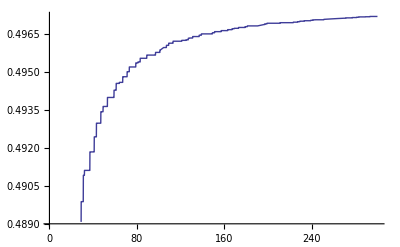

```mathematica
Plot[{S2[n]},{n,1,300}]
```

```mathematica
Integrate[ 1/( j^3 k^3 l^3 m^3),{j,1,n},{k,1,n/j}, {l,1,n/(j k)},{m,1,n/(j k l)}]
```

```mathematica
Expand[ConditionalExpression[(-3+3 n^2-6 Log[n]-6 Log[n]^2-4 Log[n]^3)/(48 n^2),Re[n]≥0||n∉Reals]]
```

ConditionalExpression[1/16-1/(16 n^2)-Log[n]/(8 n^2)-Log[n]^2/(8 n^2)-Log[n]^3/(12 n^2),Re[n]≥0||n∉Reals]